```mathematica
mat={{(ϵ^2+2 t1 ϵ ξ)/(t1 t2 ξ),(ϵ+t1 ξ)/(t1 ξ)},{(ϵ+t1 ξ)/(-t1 ξ),-t2/(t1 ξ)}}/.{ξ-> (2 t1 t2 Cos[k]-2 t1 ϵ)/(ϵ^2-t2^2)}//Simplify
```

{{(ϵ (-4 t1^2 ϵ-t2^2 ϵ+ϵ^3+4 t1^2 t2 Cos[k]))/(2 t1^2 t2 (-ϵ+t2 Cos[k])),(ϵ (2 t1^2+t2^2-ϵ^2)-2 t1^2 t2 Cos[k])/(2 t1^2 (ϵ-t2 Cos[k]))},{(-2 t1^2 ϵ-t2^2 ϵ+ϵ^3+2 t1^2 t2 Cos[k])/(2 t1^2 (ϵ-t2 Cos[k])),(t2 (t2^2-ϵ^2))/(2 t1^2 (-ϵ+t2 Cos[k]))}}

```mathematica
Eigensystem[mat]
```

{{(t2^4-4 t1^2 ϵ^2-2 t2^2 ϵ^2+ϵ^4+4 t1^2 t2 ϵ Cos[k]-√((-t2^4+4 t1^2 ϵ^2+2 t2^2 ϵ^2-ϵ^4-4 t1^2 t2 ϵ Cos[k])^2-4 (2 t1^4 t2^4+4 t1^4 t2^2 ϵ^2-8 t1^4 t2^3 ϵ Cos[k]+2 t1^4 t2^4 Cos[2 k])))/(4 t1^2 t2 (-ϵ+t2 Cos[k])),(t2^4-4 t1^2 ϵ^2-2 t2^2 ϵ^2+ϵ^4+4 t1^2 t2 ϵ Cos[k]+√((-t2^4+4 t1^2 ϵ^2+2 t2^2 ϵ^2-ϵ^4-4 t1^2 t2 ϵ Cos[k])^2-4 (2 t1^4 t2^4+4 t1^4 t2^2 ϵ^2-8 t1^4 t2^3 ϵ Cos[k]+2 t1^4 t2^4 Cos[2 k])))/(4 t1^2 t2 (-ϵ+t2 Cos[k]))},{{-((t2^4+4 t1^2 ϵ^2-ϵ^4-4 t1^2 t2 ϵ Cos[k]+√((-t2^4+4 t1^2 ϵ^2+2 t2^2 ϵ^2-ϵ^4-4 t1^2 t2 ϵ Cos[k])^2-4 (2 t1^4 t2^4+4 t1^4 t2^2 ϵ^2-8 t1^4 t2^3 ϵ Cos[k]+2 t1^4 t2^4 Cos[2 k])))/(2 t2 (2 t1^2 ϵ+t2^2 ϵ-ϵ^3-2 t1^2 t2 Cos[k]))),1},{-((t2^4+4 t1^2 ϵ^2-ϵ^4-4 t1^2 t2 ϵ Cos[k]-√((-t2^4+4 t1^2 ϵ^2+2 t2^2 ϵ^2-ϵ^4-4 t1^2 t2 ϵ Cos[k])^2-4 (2 t1^4 t2^4+4 t1^4 t2^2 ϵ^2-8 t1^4 t2^3 ϵ Cos[k]+2 t1^4 t2^4 Cos[2 k])))/(2 t2 (2 t1^2 ϵ+t2^2 ϵ-ϵ^3-2 t1^2 t2 Cos[k]))),1}}}

```mathematica
Eigensystem[mat]//Simplify
```

{{(t2^4-4 t1^2 ϵ^2-2 t2^2 ϵ^2+ϵ^4+4 t1^2 t2 ϵ Cos[k]-√(-16 t1^4 t2^2 (ϵ-t2 Cos[k])^2+(t2^4-4 t1^2 ϵ^2-2 t2^2 ϵ^2+ϵ^4+4 t1^2 t2 ϵ Cos[k])^2))/(4 t1^2 t2 (-ϵ+t2 Cos[k])),(t2^4-4 t1^2 ϵ^2-2 t2^2 ϵ^2+ϵ^4+4 t1^2 t2 ϵ Cos[k]+√(-16 t1^4 t2^2 (ϵ-t2 Cos[k])^2+(t2^4-4 t1^2 ϵ^2-2 t2^2 ϵ^2+ϵ^4+4 t1^2 t2 ϵ Cos[k])^2))/(4 t1^2 t2 (-ϵ+t2 Cos[k]))},{{-(t2^4+4 t1^2 ϵ^2-ϵ^4-4 t1^2 t2 ϵ Cos[k]+√(-16 t1^4 t2^2 (ϵ-t2 Cos[k])^2+(t2^4-4 t1^2 ϵ^2-2 t2^2 ϵ^2+ϵ^4+4 t1^2 t2 ϵ Cos[k])^2))/(2 t2 (ϵ (2 t1^2+t2^2-ϵ^2)-2 t1^2 t2 Cos[k])),1},{(-t2^4-4 t1^2 ϵ^2+ϵ^4+4 t1^2 t2 ϵ Cos[k]+√(-16 t1^4 t2^2 (ϵ-t2 Cos[k])^2+(t2^4-4 t1^2 ϵ^2-2 t2^2 ϵ^2+ϵ^4+4 t1^2 t2 ϵ Cos[k])^2))/(2 t2 (ϵ (2 t1^2+t2^2-ϵ^2)-2 t1^2 t2 Cos[k])),1}}}

```mathematica
Det[{{-(t2^4+4 t1^2 ϵ^2-ϵ^4-4 t1^2 t2 ϵ Cos[k]+√(-16 t1^4 t2^2 (ϵ-t2 Cos[k])^2+(t2^4-4 t1^2 ϵ^2-2 t2^2 ϵ^2+ϵ^4+4 t1^2 t2 ϵ Cos[k])^2))/(2 t2 (ϵ (2 t1^2+t2^2-ϵ^2)-2 t1^2 t2 Cos[k])),1},{ϵ,t2}}]//Simplify
```

(t2^4+8 t1^2 ϵ^2+2 t2^2 ϵ^2-3 ϵ^4-8 t1^2 t2 ϵ Cos[k]+√(-16 t1^4 t2^2 (ϵ-t2 Cos[k])^2+(t2^4-4 t1^2 ϵ^2-2 t2^2 ϵ^2+ϵ^4+4 t1^2 t2 ϵ Cos[k])^2))/(2 (-2 t1^2 ϵ-t2^2 ϵ+ϵ^3+2 t1^2 t2 Cos[k]))

```mathematica
Solve[(t2^4+8 t1^2 ϵ^2+2 t2^2 ϵ^2-3 ϵ^4-8 t1^2 t2 ϵ Cos[k]+√(-16 t1^4 t2^2 (ϵ-t2 Cos[k])^2+(t2^4-4 t1^2 ϵ^2-2 t2^2 ϵ^2+ϵ^4+4 t1^2 t2 ϵ Cos[k])^2))/(2 (-2 t1^2 ϵ-t2^2 ϵ+ϵ^3+2 t1^2 t2 Cos[k])),ϵ]
```

Solve::naqs: t2^4 + 8\ t1^2\ ϵ^2 + 2\ t2^2\ ϵ^2 - 3\ ϵ^4 - 8\ t1^2\ t2\ ϵ\ Cos[k] + √-16\ t1^4\ t2^2\ (ϵ + Times[« 3 »])^2 + (t2^4 - 4\ Power[« 2 »]\ Power[« 2 »] - 2\ Power[« 2 »]\ Power[« 2 »] + ϵ^4 + 4\ Power[« 2 »]\ t2\ ϵ\ Cos[« 1 »])^2/2\ (-2\ t1^2\ ϵ - t2^2\ ϵ + ϵ^3 + 2\ t1^2\ t2\ Cos[k]) is not a quantified system of equations and inequalities.

```mathematica
Solve[(t2^4+8 t1^2 ϵ^2+2 t2^2 ϵ^2-3 ϵ^4-8 t1^2 t2 ϵ Cos[k]+√(-16 t1^4 t2^2 (ϵ-t2 Cos[k])^2+(t2^4-4 t1^2 ϵ^2-2 t2^2 ϵ^2+ϵ^4+4 t1^2 t2 ϵ Cos[k])^2))/(2 (-2 t1^2 ϵ-t2^2 ϵ+ϵ^3+2 t1^2 t2 Cos[k]))==0,ϵ]
```

{{ϵ→Root[t1^2 t2^3 Cos[k]+(-t1^2 t2^2-t2^4) #1+3 t1^2 t2 Cos[k] #1^2-3 t1^2 #1^3+#1^5&,1]},{ϵ→Root[t1^2 t2^3 Cos[k]+(-t1^2 t2^2-t2^4) #1+3 t1^2 t2 Cos[k] #1^2-3 t1^2 #1^3+#1^5&,2]},{ϵ→Root[t1^2 t2^3 Cos[k]+(-t1^2 t2^2-t2^4) #1+3 t1^2 t2 Cos[k] #1^2-3 t1^2 #1^3+#1^5&,3]},{ϵ→Root[t1^2 t2^3 Cos[k]+(-t1^2 t2^2-t2^4) #1+3 t1^2 t2 Cos[k] #1^2-3 t1^2 #1^3+#1^5&,4]},{ϵ→Root[t1^2 t2^3 Cos[k]+(-t1^2 t2^2-t2^4) #1+3 t1^2 t2 Cos[k] #1^2-3 t1^2 #1^3+#1^5&,5]}}

```mathematica
With[{ϵ=Root[t1^2 t2^3 Cos[k]+(-t1^2 t2^2-t2^4) #1+3 t1^2 t2 Cos[k] #1^2-3 t1^2 #1^3+#1^5&,1],t1=500,t2=1.0},Plot[(t2^4-4 t1^2 ϵ^2-2 t2^2 ϵ^2+ϵ^4+4 t1^2 t2 ϵ Cos[k]+√(-16 t1^4 t2^2 (ϵ-t2 Cos[k])^2+(t2^4-4 t1^2 ϵ^2-2 t2^2 ϵ^2+ϵ^4+4 t1^2 t2 ϵ Cos[k])^2))/(4 t1^2 t2 (-ϵ+t2 Cos[k])),{k,-2π,2π},PlotRange-> All]]
```

-Graphics-

```mathematica
Solve[(t2^4+8 t1^2 ϵ^2+2 t2^2 ϵ^2-3 ϵ^4-8 t1^2 t2 ϵ Cos[k]+√(-16 t1^4 t2^2 (ϵ-t2 Cos[k])^2+(t2^4-4 t1^2 ϵ^2-2 t2^2 ϵ^2+ϵ^4+4 t1^2 t2 ϵ Cos[k])^2))/(2 (-2 t1^2 ϵ-t2^2 ϵ+ϵ^3+2 t1^2 t2 Cos[k]))==0,k]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{k→-ArcCos[-(ϵ (-t1^2 t2^2-t2^4-3 t1^2 ϵ^2+ϵ^4))/(t1^2 t2 (t2^2+3 ϵ^2))]},{k→ArcCos[-(ϵ (-t1^2 t2^2-t2^4-3 t1^2 ϵ^2+ϵ^4))/(t1^2 t2 (t2^2+3 ϵ^2))]}}

```mathematica
With[{k->-ArcCos[-(ϵ (-t1^2 t2^2-t2^4-3 t1^2 ϵ^2+ϵ^4))/(t1^2 t2 (t2^2+3 ϵ^2))],t1=0.5,t2=1.0},Plot[(t2^4-4 t1^2 ϵ^2-2 t2^2 ϵ^2+ϵ^4+4 t1^2 t2 ϵ Cos[k]+√(-16 t1^4 t2^2 (ϵ-t2 Cos[k])^2+(t2^4-4 t1^2 ϵ^2-2 t2^2 ϵ^2+ϵ^4+4 t1^2 t2 ϵ Cos[k])^2))/(4 t1^2 t2 (-ϵ+t2 Cos[k])),{ϵ,-10,10}]]
```

With::lvws: Variable k → -ArcCos[-ϵ\ (« 2 »\ Power[« 2 »] - Power[« 2 »] - Times[« 3 »] + ϵ^4)/Power[« 2 »]\ t2\ Plus[« 2 »]] in local variable specification {k → -ArcCos[-ϵ\ (Times[« 2 »] + Times[« 2 »] + Times[« 2 »] + Power[« 2 »])/Times[« 3 »]], t1 = 0.5, t2 = 1.} requires a value.

```mathematica
With[{t1=0.5,t2=1.0,k->-ArcCos[-(ϵ (-t1^2 t2^2-t2^4-3 t1^2 ϵ^2+ϵ^4))/(t1^2 t2 (t2^2+3 ϵ^2))]},Plot[(t2^4-4 t1^2 ϵ^2-2 t2^2 ϵ^2+ϵ^4+4 t1^2 t2 ϵ Cos[k]+√(-16 t1^4 t2^2 (ϵ-t2 Cos[k])^2+(t2^4-4 t1^2 ϵ^2-2 t2^2 ϵ^2+ϵ^4+4 t1^2 t2 ϵ Cos[k])^2))/(4 t1^2 t2 (-ϵ+t2 Cos[k])),{ϵ,-10,10}]]
```

With::lvws: Variable k → -ArcCos[-ϵ\ (« 2 »\ Power[« 2 »] - Power[« 2 »] - Times[« 3 »] + ϵ^4)/Power[« 2 »]\ t2\ Plus[« 2 »]] in local variable specification {t1 = 0.5, t2 = 1., k → -ArcCos[-ϵ\ (Times[« 2 »] + Times[« 2 »] + Times[« 2 »] + Power[« 2 »])/Times[« 3 »]]} requires a value.

With[{t1=0.5,t2=1.,k→-ArcCos[-(ϵ (-t1^2 t2^2-t2^4-3 t1^2 ϵ^2+ϵ^4))/(t1^2 t2 (t2^2+3 ϵ^2))]},Plot[(t2^4-4 t1^2 ϵ^2-2 t2^2 ϵ^2+ϵ^4+4 t1^2 t2 ϵ Cos[k]+√(-16 t1^4 t2^2 (ϵ-t2 Cos[k])^2+(t2^4-4 t1^2 ϵ^2-2 t2^2 ϵ^2+ϵ^4+4 t1^2 t2 ϵ Cos[k])^2))/(4 t1^2 t2 (-ϵ+t2 Cos[k])),{ϵ,-10,10}]]

```mathematica
(t2^4-4 t1^2 ϵ^2-2 t2^2 ϵ^2+ϵ^4+4 t1^2 t2 ϵ Cos[k]+√(-16 t1^4 t2^2 (ϵ-t2 Cos[k])^2+(t2^4-4 t1^2 ϵ^2-2 t2^2 ϵ^2+ϵ^4+4 t1^2 t2 ϵ Cos[k])^2))/(4 t1^2 t2 (-ϵ+t2 Cos[k]))/k->-ArcCos[-(ϵ (-t1^2 t2^2-t2^4-3 t1^2 ϵ^2+ϵ^4))/(t1^2 t2 (t2^2+3 ϵ^2))
```

```mathematica
(t2^4-4 t1^2 ϵ^2-2 t2^2 ϵ^2+ϵ^4+4 t1^2 t2 ϵ Cos[k]+√(-16 t1^4 t2^2 (ϵ-t2 Cos[k])^2+(t2^4-4 t1^2 ϵ^2-2 t2^2 ϵ^2+ϵ^4+4 t1^2 t2 ϵ Cos[k])^2))/(4 t1^2 t2 (-ϵ+t2 Cos[k]))/k->-ArcCos[-(ϵ (-t1^2 t2^2-t2^4-3 t1^2 ϵ^2+ϵ^4))/(t1^2 t2 (t2^2+3 ϵ^2))]
```

(t2^4-4 t1^2 ϵ^2-2 t2^2 ϵ^2+ϵ^4+4 t1^2 t2 ϵ Cos[k]+√(-16 t1^4 t2^2 (ϵ-t2 Cos[k])^2+(t2^4-4 t1^2 ϵ^2-2 t2^2 ϵ^2+ϵ^4+4 t1^2 t2 ϵ Cos[k])^2))/(4 k t1^2 t2 (-ϵ+t2 Cos[k]))→-ArcCos[-(ϵ (-t1^2 t2^2-t2^4-3 t1^2 ϵ^2+ϵ^4))/(t1^2 t2 (t2^2+3 ϵ^2))]

```mathematica
(t2^4-4 t1^2 ϵ^2-2 t2^2 ϵ^2+ϵ^4+4 t1^2 t2 ϵ Cos[k]+√(-16 t1^4 t2^2 (ϵ-t2 Cos[k])^2+(t2^4-4 t1^2 ϵ^2-2 t2^2 ϵ^2+ϵ^4+4 t1^2 t2 ϵ Cos[k])^2))/(4 t1^2 t2 (-ϵ+t2 Cos[k]))/.{k->-ArcCos[-(ϵ (-t1^2 t2^2-t2^4-3 t1^2 ϵ^2+ϵ^4))/(t1^2 t2 (t2^2+3 ϵ^2))]}
```

(t2^4-4 t1^2 ϵ^2-2 t2^2 ϵ^2+ϵ^4-(4 ϵ^2 (-t1^2 t2^2-t2^4-3 t1^2 ϵ^2+ϵ^4))/(t2^2+3 ϵ^2)+√(-16 t1^4 t2^2 (ϵ+(ϵ (-t1^2 t2^2-t2^4-3 t1^2 ϵ^2+ϵ^4))/(t1^2 (t2^2+3 ϵ^2)))^2+(t2^4-4 t1^2 ϵ^2-2 t2^2 ϵ^2+ϵ^4-(4 ϵ^2 (-t1^2 t2^2-t2^4-3 t1^2 ϵ^2+ϵ^4))/(t2^2+3 ϵ^2))^2))/(4 t1^2 t2 (-ϵ-(ϵ (-t1^2 t2^2-t2^4-3 t1^2 ϵ^2+ϵ^4))/(t1^2 (t2^2+3 ϵ^2))))

```mathematica
With[{t1=0.5,t2=1.0},Plot[{(t2^4-4 t1^2 ϵ^2-2 t2^2 ϵ^2+ϵ^4-(4 ϵ^2 (-t1^2 t2^2-t2^4-3 t1^2 ϵ^2+ϵ^4))/(t2^2+3 ϵ^2)+√(-16 t1^4 t2^2 (ϵ+(ϵ (-t1^2 t2^2-t2^4-3 t1^2 ϵ^2+ϵ^4))/(t1^2 (t2^2+3 ϵ^2)))^2+(t2^4-4 t1^2 ϵ^2-2 t2^2 ϵ^2+ϵ^4-(4 ϵ^2 (-t1^2 t2^2-t2^4-3 t1^2 ϵ^2+ϵ^4))/(t2^2+3 ϵ^2))^2))/(4 t1^2 t2 (-ϵ-(ϵ (-t1^2 t2^2-t2^4-3 t1^2 ϵ^2+ϵ^4))/(t1^2 (t2^2+3 ϵ^2))))},{ϵ,-5,5}]
```

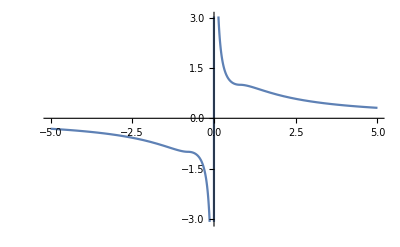

```mathematica
With[{t1=1,t2=0.8},Plot[{(t2^4-4 t1^2 ϵ^2-2 t2^2 ϵ^2+ϵ^4-(4 ϵ^2 (-t1^2 t2^2-t2^4-3 t1^2 ϵ^2+ϵ^4))/(t2^2+3 ϵ^2)+√(-16 t1^4 t2^2 (ϵ+(ϵ (-t1^2 t2^2-t2^4-3 t1^2 ϵ^2+ϵ^4))/(t1^2 (t2^2+3 ϵ^2)))^2+(t2^4-4 t1^2 ϵ^2-2 t2^2 ϵ^2+ϵ^4-(4 ϵ^2 (-t1^2 t2^2-t2^4-3 t1^2 ϵ^2+ϵ^4))/(t2^2+3 ϵ^2))^2))/(4 t1^2 t2 (-ϵ-(ϵ (-t1^2 t2^2-t2^4-3 t1^2 ϵ^2+ϵ^4))/(t1^2 (t2^2+3 ϵ^2))))},{ϵ,-5,5}]]
```

```mathematica
(t2^4-4 t1^2 ϵ^2-2 t2^2 ϵ^2+ϵ^4+4 t1^2 t2 ϵ Cos[k]+√(-16 t1^4 t2^2 (ϵ-t2 Cos[k])^2+(t2^4-4 t1^2 ϵ^2-2 t2^2 ϵ^2+ϵ^4+4 t1^2 t2 ϵ Cos[k])^2))/(4 t1^2 t2 (-ϵ+t2 Cos[k]))/.{k->ArcCos[-(ϵ (-t1^2 t2^2-t2^4-3 t1^2 ϵ^2+ϵ^4))/(t1^2 t2 (t2^2+3 ϵ^2))]}
```

(t2^4-4 t1^2 ϵ^2-2 t2^2 ϵ^2+ϵ^4-(4 ϵ^2 (-t1^2 t2^2-t2^4-3 t1^2 ϵ^2+ϵ^4))/(t2^2+3 ϵ^2)+√(-16 t1^4 t2^2 (ϵ+(ϵ (-t1^2 t2^2-t2^4-3 t1^2 ϵ^2+ϵ^4))/(t1^2 (t2^2+3 ϵ^2)))^2+(t2^4-4 t1^2 ϵ^2-2 t2^2 ϵ^2+ϵ^4-(4 ϵ^2 (-t1^2 t2^2-t2^4-3 t1^2 ϵ^2+ϵ^4))/(t2^2+3 ϵ^2))^2))/(4 t1^2 t2 (-ϵ-(ϵ (-t1^2 t2^2-t2^4-3 t1^2 ϵ^2+ϵ^4))/(t1^2 (t2^2+3 ϵ^2))))

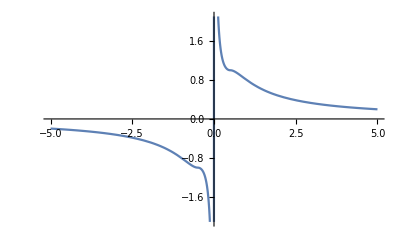

```mathematica
With[{t1=1,t2=0.5},Plot[{(t2^4-4 t1^2 ϵ^2-2 t2^2 ϵ^2+ϵ^4-(4 ϵ^2 (-t1^2 t2^2-t2^4-3 t1^2 ϵ^2+ϵ^4))/(t2^2+3 ϵ^2)+√(-16 t1^4 t2^2 (ϵ+(ϵ (-t1^2 t2^2-t2^4-3 t1^2 ϵ^2+ϵ^4))/(t1^2 (t2^2+3 ϵ^2)))^2+(t2^4-4 t1^2 ϵ^2-2 t2^2 ϵ^2+ϵ^4-(4 ϵ^2 (-t1^2 t2^2-t2^4-3 t1^2 ϵ^2+ϵ^4))/(t2^2+3 ϵ^2))^2))/(4 t1^2 t2 (-ϵ-(ϵ (-t1^2 t2^2-t2^4-3 t1^2 ϵ^2+ϵ^4))/(t1^2 (t2^2+3 ϵ^2))))},{ϵ,-5,5}]]
```

```mathematica
Det[{{(-t2^4-4 t1^2 ϵ^2+ϵ^4+4 t1^2 t2 ϵ Cos[k]+√(-16 t1^4 t2^2 (ϵ-t2 Cos[k])^2+(t2^4-4 t1^2 ϵ^2-2 t2^2 ϵ^2+ϵ^4+4 t1^2 t2 ϵ Cos[k])^2))/(2 t2 (ϵ (2 t1^2+t2^2-ϵ^2)-2 t1^2 t2 Cos[k])),1},{ϵ,t2}}]//Simplify
```

(-t2^4-8 t1^2 ϵ^2-2 t2^2 ϵ^2+3 ϵ^4+8 t1^2 t2 ϵ Cos[k]+√(-16 t1^4 t2^2 (ϵ-t2 Cos[k])^2+(t2^4-4 t1^2 ϵ^2-2 t2^2 ϵ^2+ϵ^4+4 t1^2 t2 ϵ Cos[k])^2))/(2 ϵ (2 t1^2+t2^2-ϵ^2)-4 t1^2 t2 Cos[k])

```mathematica
Solve[(-t2^4-8 t1^2 ϵ^2-2 t2^2 ϵ^2+3 ϵ^4+8 t1^2 t2 ϵ Cos[k]+√(-16 t1^4 t2^2 (ϵ-t2 Cos[k])^2+(t2^4-4 t1^2 ϵ^2-2 t2^2 ϵ^2+ϵ^4+4 t1^2 t2 ϵ Cos[k])^2))/(2 ϵ (2 t1^2+t2^2-ϵ^2)-4 t1^2 t2 Cos[k])==0,k]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{k→-ArcCos[-(ϵ (-t1^2 t2^2-t2^4-3 t1^2 ϵ^2+ϵ^4))/(t1^2 t2 (t2^2+3 ϵ^2))]},{k→ArcCos[-(ϵ (-t1^2 t2^2-t2^4-3 t1^2 ϵ^2+ϵ^4))/(t1^2 t2 (t2^2+3 ϵ^2))]}}

```mathematica
(t2^4-4 t1^2 ϵ^2-2 t2^2 ϵ^2+ϵ^4+4 t1^2 t2 ϵ Cos[k]+√(-16 t1^4 t2^2 (ϵ-t2 Cos[k])^2+(t2^4-4 t1^2 ϵ^2-2 t2^2 ϵ^2+ϵ^4+4 t1^2 t2 ϵ Cos[k])^2))/(4 t1^2 t2 (-ϵ+t2 Cos[k]))/.{k->-ArcCos[-(ϵ (-t1^2 t2^2-t2^4-3 t1^2 ϵ^2+ϵ^4))/(t1^2 t2 (t2^2+3 ϵ^2))]}
```

(t2^4-4 t1^2 ϵ^2-2 t2^2 ϵ^2+ϵ^4-(4 ϵ^2 (-t1^2 t2^2-t2^4-3 t1^2 ϵ^2+ϵ^4))/(t2^2+3 ϵ^2)+√(-16 t1^4 t2^2 (ϵ+(ϵ (-t1^2 t2^2-t2^4-3 t1^2 ϵ^2+ϵ^4))/(t1^2 (t2^2+3 ϵ^2)))^2+(t2^4-4 t1^2 ϵ^2-2 t2^2 ϵ^2+ϵ^4-(4 ϵ^2 (-t1^2 t2^2-t2^4-3 t1^2 ϵ^2+ϵ^4))/(t2^2+3 ϵ^2))^2))/(4 t1^2 t2 (-ϵ-(ϵ (-t1^2 t2^2-t2^4-3 t1^2 ϵ^2+ϵ^4))/(t1^2 (t2^2+3 ϵ^2))))

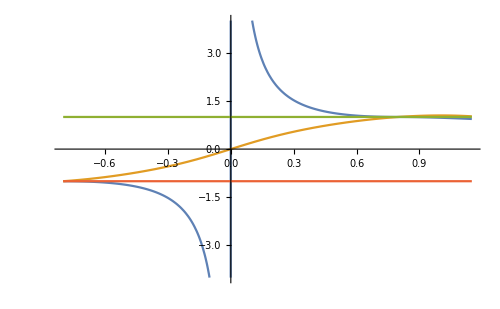

```mathematica
With[{t1=1.0,t2=0.8},Plot[{(t2^4-4 t1^2 ϵ^2-2 t2^2 ϵ^2+ϵ^4-(4 ϵ^2 (-t1^2 t2^2-t2^4-3 t1^2 ϵ^2+ϵ^4))/(t2^2+3 ϵ^2)+√(-16 t1^4 t2^2 (ϵ+(ϵ (-t1^2 t2^2-t2^4-3 t1^2 ϵ^2+ϵ^4))/(t1^2 (t2^2+3 ϵ^2)))^2+(t2^4-4 t1^2 ϵ^2-2 t2^2 ϵ^2+ϵ^4-(4 ϵ^2 (-t1^2 t2^2-t2^4-3 t1^2 ϵ^2+ϵ^4))/(t2^2+3 ϵ^2))^2))/(4 t1^2 t2 (-ϵ-(ϵ (-t1^2 t2^2-t2^4-3 t1^2 ϵ^2+ϵ^4))/(t1^2 (t2^2+3 ϵ^2)))),-(ϵ (-t1^2 t2^2-t2^4-3 t1^2 ϵ^2+ϵ^4))/(t1^2 t2 (t2^2+3 ϵ^2)),1,-1},{ϵ,-.8,1.15}]]
```